```mathematica
α=3/4;
```

```mathematica
Clear[α];
```

```mathematica
f[x_,a_,b_,c_,σ_]:=(1-α)*Abs[x^(α-2)]*Exp[-(x^(α-1)-a/c)^2/(2*σ^2*b^2/c^2)]/Sqrt[2*Pi*σ^2*b^2/c^2];
```

```mathematica
Integrate[f[x],{x,0,Infinity}, Assumptions->a>0 && b>0&&c>0&&σ>0&&α==-10000.5]
```

1/2 (1+Erf[a/(√2 b σ)])

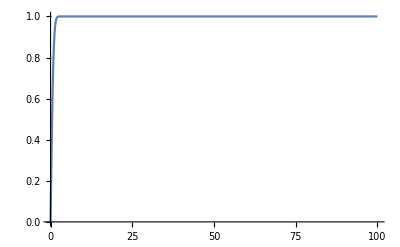

```mathematica
Plot[Erf[x],{x,0,100}]
```